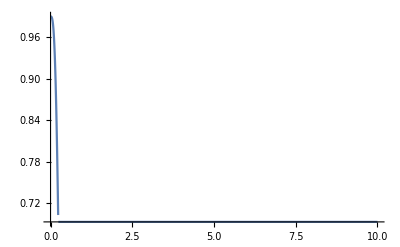

```mathematica
(*remaps interval [0; inf) to [0.7, 0.99]*)
MyRemapFunc[x_]:=((Max[Exp[-(x*3)^3],0.7])*0.99)
Plot[MyRemapFunc[x],{x,0,10},PlotRange->Full]
```

```mathematica
GetRandom[]:=RandomVariate[NormalDistribution[0,0.2],1][[1]];
values=Table[GetRandom[]+(UnitStep[i-1000]-UnitStep[i-2000])*Sin[i/50]+2+i/1500*UnitStep[i-2000]*5,{i,3000}];
```

General::munfl: Exp[-1173.75] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4663.45] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9321.38] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

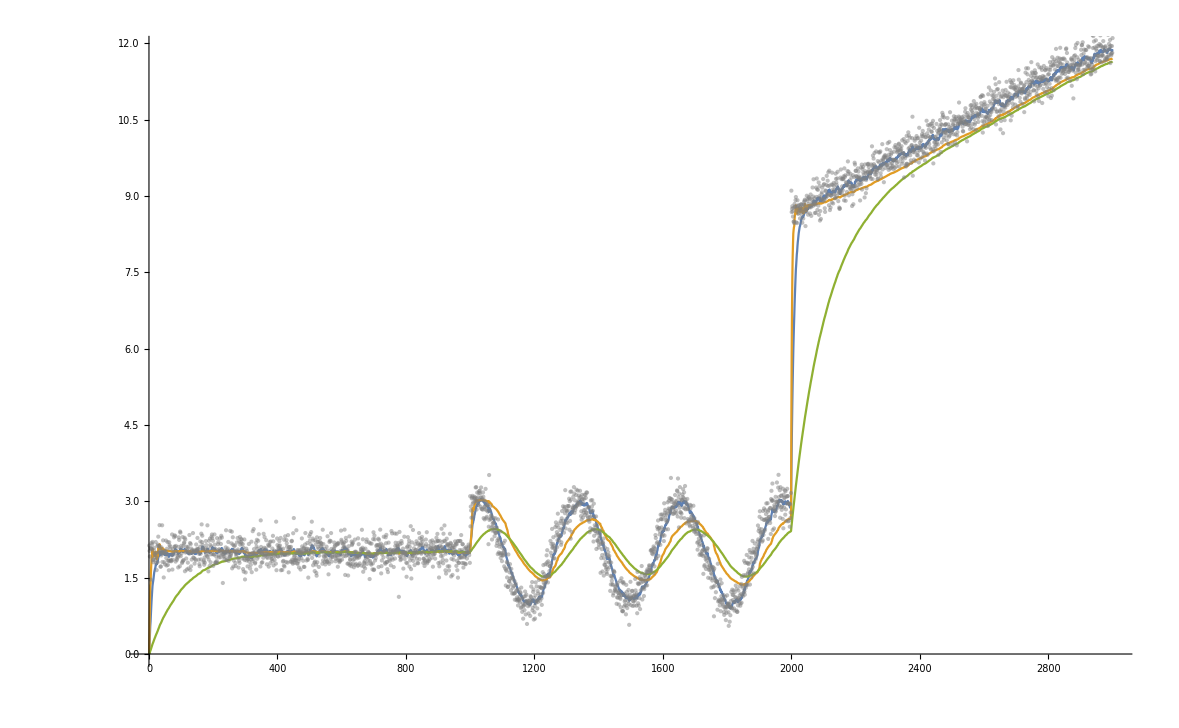

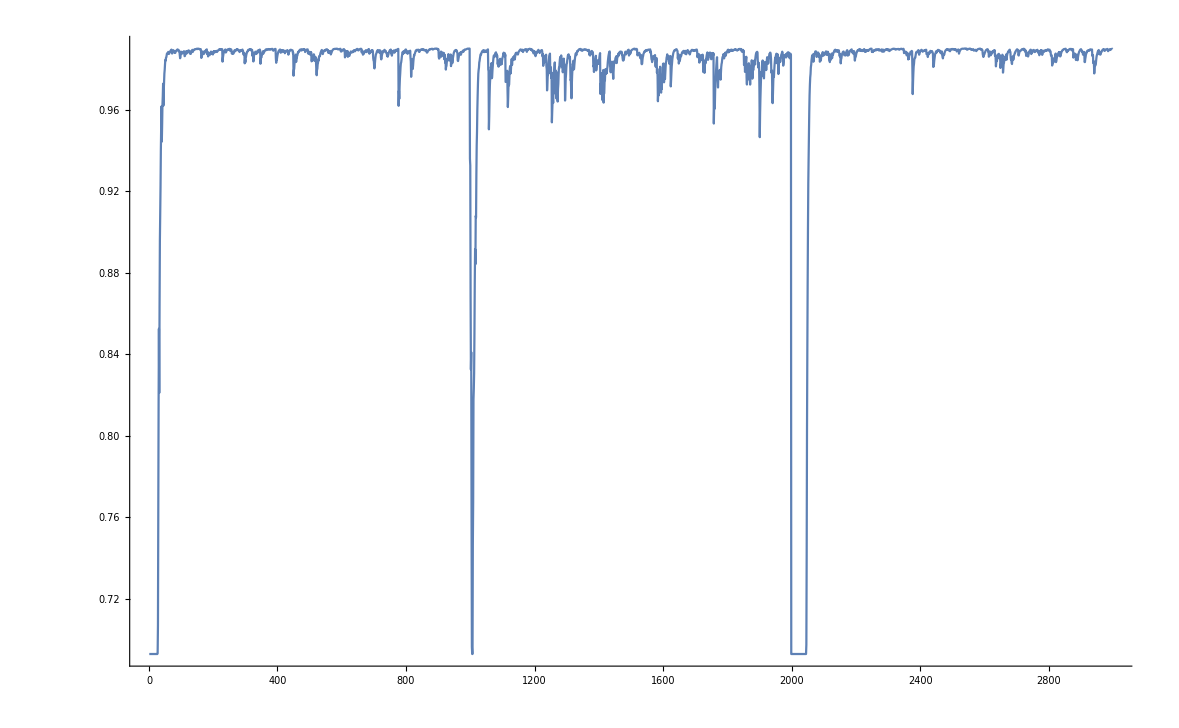

```mathematica
emaLong={0};
ema={0};
emaSquared={0};
updatedWeights={};
improvedEma={0};
hysteresis=0.9;
longHysteresis=0.99;
For[i=2,i≤Length[values],++i,
currentAvg=(avg[[i-1]]*(i-1)+values[[i]])/i;
AppendTo[avg,currentAvg];
currentEma=ema[[i-1]]*(hysteresis)+values[[i]]*(1-hysteresis);
AppendTo[ema,currentEma];
currentEmaLong=emaLong[[i-1]]*(longHysteresis)+values[[i]]*(1-longHysteresis);
AppendTo[emaLong,currentEmaLong];
currentEmaSquared=emaSquared[[i-1]]*(hysteresis)+values[[i]]^2*(1-hysteresis);
AppendTo[emaSquared,currentEmaSquared];
variance=currentEmaSquared-currentEma^2;
currentHysteresis=MyRemapFunc[variance];
currentImprovedEma=improvedEma[[i-1]]*(currentHysteresis)+values[[i]]*(1-currentHysteresis);
AppendTo[improvedEma,currentImprovedEma];
AppendTo[updatedWeights,currentHysteresis];
]

Show[ListLinePlot[{ema,improvedEma,emaLong},PlotRange->Full],ListPlot[values,PlotStyle->{PointSize[Small],Opacity[0.5],Gray}]]

ListLinePlot[updatedWeights,PlotRange->Full]
```